# Homework_Problems

```mathematica
Create a list (10x10) of random numbers
a)Express the output in traditional form
     b) Extract the first 10 random numbers
	c)  Extract the last number in the list
```

```mathematica
(*Output in Traditional Form*)
listNumbers=RandomReal[5,{10,10}];
listNumbers // TraditionalForm
```

(1.08158 | 1.98027 | 0.22199 | 1.15659 | 4.62893 | 3.4805 | 0.0679939 | 1.52402 | 4.22335 | 2.74257
2.09307 | 1.92681 | 1.90517 | 1.67482 | 3.45174 | 4.70233 | 3.05211 | 0.142459 | 4.09783 | 1.37525
3.73206 | 3.11428 | 3.02093 | 0.487296 | 4.61363 | 4.40053 | 0.899183 | 0.582599 | 4.52336 | 1.90152
1.05967 | 1.09608 | 3.15845 | 2.82206 | 3.21998 | 4.52049 | 3.44457 | 2.25979 | 0.077914 | 1.08675
3.69762 | 0.729639 | 4.40015 | 1.04816 | 2.5544 | 1.94331 | 3.12584 | 1.41665 | 1.48276 | 1.68245
3.97355 | 3.61265 | 4.9306 | 2.66395 | 3.42332 | 2.58655 | 4.73568 | 3.42839 | 2.93513 | 4.00794
3.3863 | 0.450632 | 2.98215 | 3.56066 | 1.98689 | 0.322966 | 3.57098 | 3.35619 | 0.878447 | 3.38322
4.70169 | 4.27219 | 2.96841 | 1.10083 | 0.907409 | 2.81383 | 3.9734 | 1.93597 | 4.54438 | 2.88263
3.91677 | 4.84741 | 2.91736 | 4.47453 | 2.35242 | 1.13541 | 4.04306 | 0.996151 | 4.65698 | 1.20784
1.22923 | 1.85623 | 2.88537 | 1.41176 | 4.09552 | 3.51592 | 0.939869 | 3.68855 | 1.36717 | 4.91113)

```mathematica
(*First 10 random numbers*)
listNumbers[[1]]
```

{1.08158,1.98027,0.22199,1.15659,4.62893,3.4805,0.0679939,1.52402,4.22335,2.74257}

```mathematica
(*Last Number in the list*)
Last[Last[listNumbers]]
```

4.91113

Find the dot product of the vector ~a and~b, where ~a = 2i+7j+15k and~b = αi+βj+γk

```mathematica
{2,7,15}.{α,β,γ}
```

2 α+7 β+15 γ

Define two 3x3 matrices using the function Table
(a) Find the product of matrices
(b) Find the inverse of the resultant matrix
(c) Find the determinant and eigenvalues of the matrix

```mathematica
A = Table[RandomInteger[10],3,3];
B = Table[RandomInteger[10],3,3];
```

```mathematica
Grid[A]
Grid[B]
```

3 | 8 | 6
9 | 2 | 7
4 | 5 | 7

1 | 10 | 10
1 | 10 | 2
3 | 3 | 8

```mathematica
ResultMatrix = A.B;
Grid[ResultMatrix]
```

29 | 128 | 94
32 | 131 | 150
30 | 111 | 106

```mathematica
InvMatrix = Inverse[ResultMatrix];
Grid[InvMatrix]
```

-691/6534 | -1567/13068 | 313/1188
277/6534 | 127/13068 | -61/1188
-7/484 | 23/968 | -1/88

```mathematica
Det[InvMatrix]
```

1/26136

```mathematica
Eigenvalues[ResultMatrix]
```

{Root276.Root[-26136-2807 #1-266 #1^2+#1^3&,1]276.49399452720917,Root-5.25+8.19 ⅈRoot[-26136-2807 #1-266 #1^2+#1^3&,3]-5.2469972636045945,Root-5.25-8.19 ⅈRoot[-26136-2807 #1-266 #1^2+#1^3&,2]-5.2469972636045945}

Solve the following diffrential equations
(a) d
2y
dx2 = 2x + y +
dy
dx with y(2) = 1 and y
0
(2) = −1

(b) d
2y
dx2 + Sin2
(x)
dy
dx + 3y
2 = e
−x
2
with y(0) = 1 and y
0
(0) = 0

(c) Plot the solutions

```mathematica
eqn1 = {y''[x] == 2*x + y[x]  + y'[x], y[2]==1, y'[2]==-1};
sol1 = DSolve[eqn1,y[x],x];
```

```mathematica
sol1
```

{{y[x]→1/10 ⅇ^(-1-√5) (20 ⅇ^(1+√5)+15 ⅇ^((1/2+(√5)/2) x)-√5 ⅇ^((1/2+(√5)/2) x)+15 ⅇ^(2 √5+(1/2-(√5)/2) x)+√5 ⅇ^(2 √5+(1/2-(√5)/2) x)-20 ⅇ^(1+√5) x)}}

```mathematica
eqn0 = {y'[x]==y[x],y[0]==1};
sol0=DSolve[eqn0,y[x],x];
sol0;
```

```mathematica
eqn2 = {y''[x] + (((Sin [x])^2 )*y'[x])+  3(y[x])^2 ==  Exp[-(x^2)], y[0]==1, y'[0]==0};
eqn2
```

{3 y[x]^2+Sin[x]^2 y'[x]+y''[x]==ⅇ^(-x^2),y[0]==1,y'[0]==0}

```mathematica
DSolve[eqn2,y[x],x];
```

```mathematica
NDSolve[{3 y[x]^2+Sin[x]^2 y'[x]+y''[x]==ⅇ^(-x^2),y[0]==1,y'[0]==0},y[x],{x, -10,10}]
```

NDSolve::ndsz: At x == -2.89065, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 5.17319, step size is effectively zero; singularity or stiff system suspected.

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
%322⟦1,1,2⟧
```

InterpolatingFunction[…][x]

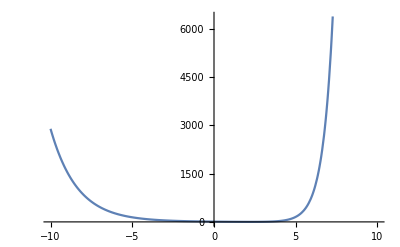

y[x]

```mathematica
Plot[y[x]/.sol1,{x, -10,10}]
```